## Setup

```mathematica
f[{x_,y_}]=ⅇ^(-(x+y)^2)+x^2-Cos[x y]+Sin[10x y^2]-0.5;
f[{{x_},{y_}}]=f[{x,y}];
dx=0.001;
dy=0.001;
fx=(f[{x+dx,y}]-f[{x-dx,y}])/(2dx)//FullSimplify;
fy=(f[{x,y+dy}]-f[{x,y-dy}])/(2dy)//FullSimplify;
fxx=(f[{x+dx,y}]-2f[{x,y}]+f[{x-dx,y}])/dx^2//FullSimplify;
fyy=(f[{x,y+dy}]-2f[{x,y}]+f[{x,y-dy}])/dy^2//FullSimplify;
fxy=(f[{x+dx,y+dy}]-f[{x+dx,y-dy}]-f[{x-dx,y+dy}]+f[{x-dx,y-dy}])/(4dx dy)//FullSimplify;
gradf[{{x_},{y_}}]=({{fx}, {fy}});
H[{{x_},{y_}}]=({{fxx, fxy}, {fxy, fyy}});
invH[{{x_},{y_}}]=Inverse[H[{{x},{y}}]];
```

$Aborted

### Initial Solution Guess

```mathematica
X=({{0.2}, {0.2}});
```

## Newton’s Optimization Method

```mathematica
Do[
X=X-0.01LinearSolve[H[X],gradf[X]];,
{i,10}]
Norm[X]
H[X]//N//MatrixForm
```

0.699808

(-2. | 0.
0. | -2.)

## Gradient Descent

```mathematica
Do[
X=X-0.001gradf[X];,
{i,1000}]
X
Norm[X]
H[X]//N//MatrixForm
```

{{0.706194},{0.706194}}

0.998709

(-2. | 122.774
122.774 | -2.)

## 1D Newton’s Method Along Normal Direction

```mathematica
f[{x_,y_}]=√(x^2+y^2)-1;
dx=0.01;
dy=0.01;
fx=(f[{x+dx,y}]-f[{x-dx,y}])/(2dx)//FullSimplify;
fy=(f[{x,y+dy}]-f[{x,y-dy}])/(2dy)//FullSimplify;
gradf[{x_,y_}]={fx,fy};
```

1.

{0.447216,0.894426}

6.32892×10^-11

2

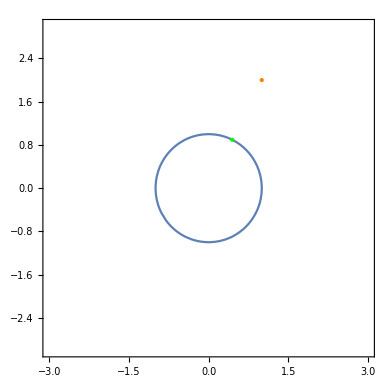

```mathematica
init=X={1,2};
counter=0;
While[Abs[f[X]]>10^-10,
X=X-f[X]/Norm[gradf[X]]^2 gradf[X];
counter=counter+1]
Norm[X]
pt=X//Flatten
f[X]
counter
Show[ContourPlot[f[{x,y}]==0,
{x,-3,3},{y,-3,3},
Contours->20],
Graphics[{
{PointSize[Large],Green,Point[pt]},
{PointSize[Large],Orange,Point[init//Flatten]}}]]
```